```mathematica
OpenRead[FileNameJoin[{NotebookDirectory[],"graphs_database.m"}]];
graphsVerticesEdges=Read[FileNameJoin[{NotebookDirectory[],"graphs_database.m"}]];
Close[FileNameJoin[{NotebookDirectory[],"graphs_database.m"}]];
graphsAll=Map[Graph[#[[1]],#[[2]]]&,graphsVerticesEdges,{2}];
```

```mathematica
ClearAll[edgeContract]
edgeContract[graph_,edge_]:=Module[{ec=EdgeContract[graph,edge],v=VertexList[{edge}],t=Total[PropertyValue[{graph,#},VertexWeight]&/@VertexList[{edge}]]},SetProperty[ec,VertexWeight->Join[#->PropertyValue[{graph,#},VertexWeight]&/@Complement[VertexList[graph],v],{v[[1]]->t,v[[2]]->t}]]]
```

```mathematica
wPolynomial[graph_]:=Module[{e},
If[EmptyGraphQ[graph],
varList=Subscript[q,#]&/@PropertyValue[graph,VertexWeight];
Return[Times@@varList],
Return[wPolynomial[EdgeDelete[graph,e=EdgeList[graph][[1]]]]+wPolynomial[edgeContract[graph,e]]]
]];
```

```mathematica
whFunction[n_]:=Module[{i,l},
graphs=graphsAll[[n]];
l=Length[graphs];
For[i=1,i≤l,++i,graphs[[i]]=SetProperty[graphs[[i]],VertexWeight->Array[1&,VertexCount[graphs[[i]]]]]];
w=0;
For[i=1,i≤l,++i,
(* Comment or uncomment if ConnectedGraphQ statement *)
If[ConnectedGraphQ[graphs[[i]]],w=w+(h^(Length[VertexList[graphs[[i]]]]-Length[EdgeList[graphs[[i]]]]))*wPolynomial[graphs[[i]]]/(GroupOrder[GraphAutomorphismGroup[graphs[[i]]]])
]
];
Return[Expand[w]]]
```

```mathematica
(* Connected Graphs *)
```

```mathematica
(* c_{0;n} n=1,...,8 *)
```

```mathematica
coeff={0,0,1/3,11/8,22/5,155/12,6127/168,293/16};
model=NonlinearModelFit[coeff,a*x^b,{a,b},x]
```

FittedModel[0.19178 x^2.38648]

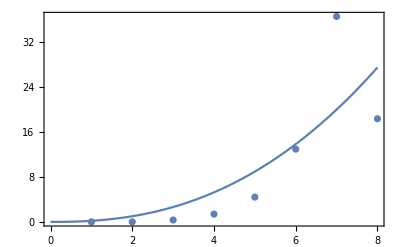

```mathematica
Show[ListPlot[coeff],Plot[model[x],{x,0,8}],Frame->True]
```

```mathematica
(* c_{0;n-1,1} n=2,...,8 *)
```

```mathematica
coeff2={0,1/2,5/2,19/2,389/12,209/2,173/4};
model2=NonlinearModelFit[coeff2,a*x^b,{a,b},x]
```

FittedModel[1.55551 x^1.96828]

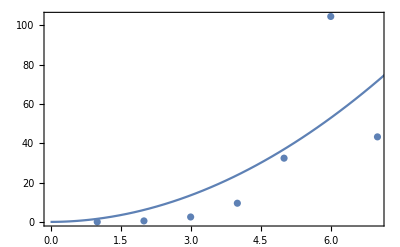

```mathematica
Show[ListPlot[coeff2],Plot[model2[x],{x,0,8}],Frame->True]
```

```mathematica
(* c_{0;n-2,1,1} n=3,...,8 *)
```

```mathematica
coeff3={1/6,5/2,43/4,251/6,7321/48,219/4};
model3=NonlinearModelFit[coeff3,a*x^b,{a,b},x]
```

FittedModel[5.82459 x^1.57672]

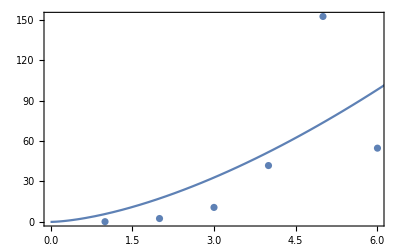

```mathematica
Show[ListPlot[coeff3],Plot[model3[x],{x,0,8}],Frame->True]
```